```mathematica
trainSet=Import["/Users/nguyen/Documents/mnist_trained_set_30deg.mx"];
```

```mathematica
leNet=NetTrain[NetModel["LeNet"],trainSet,ValidationSet->Scaled[0.2]]
```

NetChain[<>]

```mathematica
Export["/Users/nguyen/Documents/leNetTrain.wlnet",leNet];
```

```mathematica
testSet=Import["/Users/nguyen/Documents/mnist_test_set_30deg.mx"];
```

```mathematica
res=ClassifierMeasurements[leNet,testSet];
```

```mathematica
res["Accuracy"]
```

0.977367

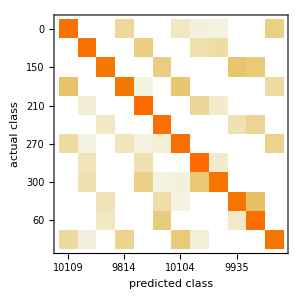

```mathematica
res["ConfusionMatrixPlot"]
```